### Start choosing the example:

```mathematica
t=25
```

25

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];
MFGEquations["criticalreduced"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

First reduced: {NonNegative[j388]&&NonNegative[2-j388]&&NonNegative[2-j388]&&NonNegative[j388]&&NonNegative[j388]&&NonNegative[j388]&&NonNegative[2-j388]&&NonNegative[2-j388]&&NonNegative[1-u403]&&NonNegative[-u405+u408]&&NonNegative[-u407+u408]&&NonNegative[u405-u408]&&NonNegative[u405-u407]&&NonNegative[5-u410]&&(j388==0||-1+u403==0)&&(j388==0||u407-u408==0)&&(2-j388==0||-u405+u407==0)&&(2-j388==0||-5+u410==0),<|j387→2,u409→1,u411→5,j383→0,j384→j388,j385→2-j388,j386→2-j388,j389→0,j390→0,j391→0,j392→0,jt393→j388,jt394→0,jt395→0,jt396→0,jt397→0,jt398→0,jt399→j388,jt400→2-j388,jt401→2-j388,jt402→0,u404→1,u406→5,u412→u407|>}

Reduce on the above system: (u410<5&&u403==1&&j388==2&&u407==u408&&u405==u408)||(u410==5&&((u403<1&&j388==0&&u407==u408&&u405==u408)||(u403==1&&0≤j388≤2&&u407==u408&&u405==u408)))

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

DataToEquations: Critical case ...

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

DataToEquations: Reducing ...

EqEliminatorX: Reached a solution!

DataToEquations: Done.

<|j383→0,j384→2,j385→2-2,j386→2-2,j387→2,j388→2,j389→0,j390→0,j391→0,j392→0,jt393→2,jt394→0,jt395→0,jt396→0,jt397→0,jt398→0,jt399→2,jt400→2-2,jt401→2-2,jt402→0,u403→1,u404→1,u405→3,u406→5,u407→3,u408→2+1,u409→1,u410→-2+2+3,u411→5,u412→3|>

#### Non-linear case

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];
nsol=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],20, SameTest-> (Norm[(#1-#2)//Values]<10^(-9)&)]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

DataToEquations: Critical case ...

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

DataToEquations: Reducing ...

EqEliminatorX: Reached a solution!

DataToEquations: Done.

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

Eliminator: System is not True and Head of system is NOT And or Or. Returning the input.

EqEliminatorX: Reached a solution!

<|j189→2,u211→1,u213→5,j185→0,j186→2.,j187→2-2.,j188→2-2.,j191→0,j192→0,j193→0,j194→0,jt195→2.,jt196→0,jt197→0,jt198→0,jt199→0,jt200→0,jt201→2.,jt202→2-2.,jt203→2-2.,jt204→0,u206→1,u208→5,u214→2.67538,u210→-0.324624+1. 2.+1. 1.,u212→-2.+1. 2.+1. 2.67538,j190→2.,u205→1.,u207→2.67538,u209→2.67538|>

### What we this plot for?

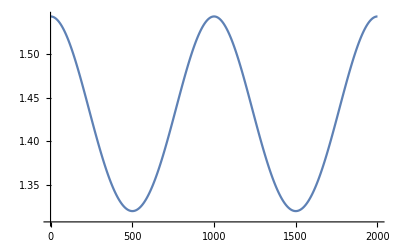

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.

### New alternative to solving the equations

```mathematica
AA=MFGEquations["EqAllAll"];
NN=Select[AA,Head[#]===NonNegative&];
OO = Select[AA,Head[#]===Or&];
EE=Select[AA,Head[#]===Equal&];
Timing[Simplify[NN];](*note the semi-colon!*)
Timing[FullSimplify[NN];]
Timing[Reduce[NN,Reals];](*Takes more time, but shows the equalities.*)
```

{0.00012,Null}

{0.000111,Null}

{0.00917,Null}

#### this shows that we did not throw equations away! At least before using Reduce!

```mathematica
(MFGEquations["EqAllAll"]//Sort)===(NN&&EE&&OO//Sort)
```

True

### One iteration to solve the critical congestion case:

```mathematica
rdcd=EqEliminatorX2[{MFGEquations["EqAllAll"]&&MFGEquations["EqCriticalCase"], MFGEquations["BoundaryRules"]}]
```

{(j322==0||j317==0)&&(j323==0||j318==0)&&(j324==0||j319==0)&&(j325==0||j320==0)&&(jt327==0||jt328==0)&&(jt329==0||jt331==0)&&(jt330==0||jt333==0)&&(jt332==0||jt334==0)&&(jt335==0||jt336==0)&&(jt327==0||u337-u338==0)&&(jt329==0||-u339+u342==0)&&(jt331==0||u339-u342==0)&&(jt333==0||-u342+u346==0)&&(jt334==0||-u339+u346==0)&&(jt335==0||-u340+u344==0),NonNegative[j317]&&NonNegative[j318]&&NonNegative[j319]&&NonNegative[j320]&&NonNegative[j322]&&NonNegative[j323]&&NonNegative[j324]&&NonNegative[j325]&&NonNegative[j326]&&NonNegative[jt327]&&NonNegative[jt328]&&NonNegative[jt329]&&NonNegative[jt330]&&NonNegative[jt331]&&NonNegative[jt332]&&NonNegative[jt333]&&NonNegative[jt334]&&NonNegative[jt335]&&NonNegative[jt336]&&NonNegative[-u337+u338]&&NonNegative[-u339+u342]&&NonNegative[u342-u346]&&NonNegative[u339-u342]&&NonNegative[u339-u346]&&NonNegative[u340-u344],j322==jt327&&j323==jt328&&j317==jt329+jt330&&j324==jt331+jt332&&2==jt333+jt334&&j319==jt335&&j325==jt336&&j317==jt328&&j318==jt327&&j322==jt331+jt333&&j319==jt329+jt334&&j326==jt330+jt332&&j324==jt336&&j320==jt335&&-u341+u346==0&&1-u338==0&&5-u340==0&&j326==0&&jt328==0&&jt330==0&&jt332==0&&jt336==0&&-j322-u337+u342==0&&2-j322-u339+u344==0,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u342→j322+u337,u344→-2+j322+u339,u346→u341|>}

```mathematica
m=4;rdcd2=FixedPointList[EqEliminatorX2,rdcd,m]
```

{{(j322==0||j317==0)&&(j323==0||j318==0)&&(j324==0||j319==0)&&(j325==0||j320==0)&&(jt327==0||jt328==0)&&(jt329==0||jt331==0)&&(jt330==0||jt333==0)&&(jt332==0||jt334==0)&&(jt335==0||jt336==0)&&(jt327==0||u337-u338==0)&&(jt329==0||-u339+u342==0)&&(jt331==0||u339-u342==0)&&(jt333==0||-u342+u346==0)&&(jt334==0||-u339+u346==0)&&(jt335==0||-u340+u344==0),NonNegative[j317]&&NonNegative[j318]&&NonNegative[j319]&&NonNegative[j320]&&NonNegative[j322]&&NonNegative[j323]&&NonNegative[j324]&&NonNegative[j325]&&NonNegative[j326]&&NonNegative[jt327]&&NonNegative[jt328]&&NonNegative[jt329]&&NonNegative[jt330]&&NonNegative[jt331]&&NonNegative[jt332]&&NonNegative[jt333]&&NonNegative[jt334]&&NonNegative[jt335]&&NonNegative[jt336]&&NonNegative[-u337+u338]&&NonNegative[-u339+u342]&&NonNegative[u342-u346]&&NonNegative[u339-u342]&&NonNegative[u339-u346]&&NonNegative[u340-u344],j322==jt327&&j323==jt328&&j317==jt329+jt330&&j324==jt331+jt332&&2==jt333+jt334&&j319==jt335&&j325==jt336&&j317==jt328&&j318==jt327&&j322==jt331+jt333&&j319==jt329+jt334&&j326==jt330+jt332&&j324==jt336&&j320==jt335&&-u341+u346==0&&1-u338==0&&5-u340==0&&j326==0&&jt328==0&&jt330==0&&jt332==0&&jt336==0&&-j322-u337+u342==0&&2-j322-u339+u344==0,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u342→j322+u337,u344→-2+j322+u339,u346→u341|>},{(j322==0||-1+u337==0)&&(j322==0||-j322-u337+u341==0)&&(2-j322==0||-u339+u341==0)&&(2-j322==0||-7+j322+u339==0),u341==3&&u339==3&&u337==1&&j322==2,u341==3&&u339==3&&u337==1&&j322==2,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u342→j322+u337,u344→-2+j322+u339,u346→u341,j322→2,u337→1,u339→3,u341→3|>},{True,True,True,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u342→j322+u337,u344→-2+j322+u339,u346→u341,j322→2,u337→1,u339→3,u341→3|>},{True,True,True,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u342→j322+u337,u344→-2+j322+u339,u346→u341,j322→2,u337→1,u339→3,u341→3|>}}

```mathematica
EqEliminatorX2[{MFGEquations["reduced"][[1]]&&MFGEquations["EqCriticalCase"], MFGEquations["reduced"][[2]]}]
```

{(u344<5&&u337==1&&j322==2&&u341==u342&&u339==u342)||(u344==5&&((u337<1&&j322==0&&u341==u342&&u339==u342)||(u337==1&&0≤j322≤2&&u341==u342&&u339==u342))),True,-j322-u337+u342==0&&2-j322-u339+u344==0,<|j321→2,u343→1,u345→5,j317→0,j318→j322,j319→2-j322,j320→2-j322,j323→0,j324→0,j325→0,j326→0,jt327→j322,jt328→0,jt329→0,jt330→0,jt331→0,jt332→0,jt333→j322,jt334→2-j322,jt335→2-j322,jt336→0,u338→1,u340→5,u346→u341,u342→j322+u337,u344→-2+j322+u339|>}

```mathematica
Reduce[And @@(FullSimplify[rdcd[[2]]/.rdcd[[4]]][[#]]&/@Range[3]),Reals]
```

0≤j256≤2&&u271≤1

```mathematica
rdcd2
```